Ce notebook mathematica produit le fichier cs.in qui sera lu par MDFT dans le cas d’une fonctionnelle perturbation basée sur Vlj sans sa partie répulsive.

```mathematica
σ=3.7327;ϵ=1.247;
```

```mathematica
ϕ[r_]:=4ϵ((σ/r)^12-(σ/r)^6)
ϕa[r_?NumberQ]:=Piecewise[{{-ϵ,r<2^(1/6)σ},{4ϵ((σ/r)^12-(σ/r)^6),r≥ 2^(1/6)σ}}]
```

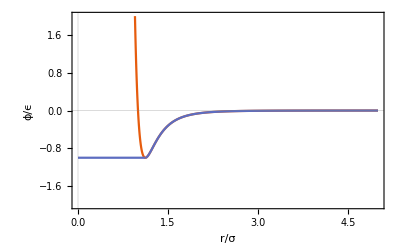

```mathematica
Plot[{ϕ[r*σ]/ϵ,Evaluate[ϕa[r]/ϵ/.σ->1]},{r,0,5},PlotTheme->"Scientific",PlotRange->{-2,2},FrameLabel->{"r/σ","ϕ/ϵ"},LabelStyle->Medium]
```

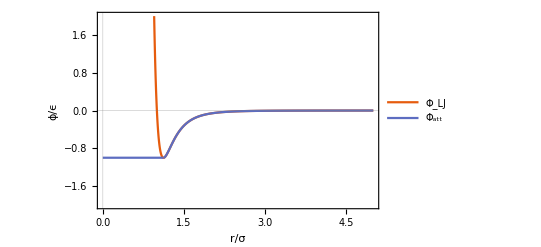

```mathematica
Plot[{ϕ[r σ]/ϵ,Evaluate[ϕa[r]/ϵ/.σ->1]},{r,0,5},PlotTheme->"Scientific",PlotRange->{-2,2},FrameLabel->{"r/σ","ϕ/ϵ"},LabelStyle->Medium,PlotLegends->Automatic]
```

```mathematica
Clear[ϕak];
ϕak[k_]:=ϕak[k]=Piecewise[{
{4π NIntegrate[r^2*ϕa[r],{r,0,∞}],k==0},
{4π NIntegrate[r^2*Sin[k*r]/(k*r)*ϕa[r],{r,0,∞}],k>0}
}];
```

```mathematica
(* for LJ potential, note that     Integrate[r^2*lja[r],{r,0,∞}]= -8/9 √2 ϵ σ^3 for k==0  *)
```

```mathematica
Quiet@Plot[ϕak[k],{k,0,3},PlotRange->Full,PerformanceGoal->"Speed",PlotTheme->"Monochrome",AxesLabel->{"k/Å^-1","ϕ_att(k)/kJ·mol^-1·Å^-1"},ImageSize->Large,LabelStyle->Medium]
```

NIntegrate::inumr: The integrand r^2\ (TagBox[GridBox[{{"{", GridBox[{{-ϵ, r < 2^1/6\ σ}, {4\ ϵ\ (-Power[« 2 »]\ Power[« 2 »] + Power[« 2 »]\ Power[« 2 »]), r ≥ 2^1/6\ σ}, {"0", TagBox["True", "PiecewiseDefault", Rule[AutoDelete, True]]}}, ColumnAlignments -> {Left}, ColumnSpacings -> 1.2, ColumnWidths -> Automatic, AllowedDimensions -> {2, Automatic}, Selectable -> True, Editable -> True]}}, ColumnAlignments -> {Left}, ColumnSpacings -> 0.5, ColumnWidths -> Automatic], "Piecewise", Rule[SyntaxForm, Equal], Rule[SelectWithContents, True], Rule[Selectable, False], Rule[Editable, False], Rule[DeleteWithContents, True]]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand 7992.01\ (0.  + r)\ (TagBox[GridBox[{{"{", GridBox[{{-ϵ, 0.  + r < 2^1/6\ σ}, {4\ ϵ\ (-Power[« 2 »]\ Power[« 2 »] + Power[« 2 »]\ Power[« 2 »]), 0.  + r ≥ 2^1/6\ σ}, {"0", TagBox["True", "PiecewiseDefault", Rule[AutoDelete, True]]}}, ColumnAlignments -> {Left}, ColumnSpacings -> 1.2, ColumnWidths -> Automatic, AllowedDimensions -> {2, Automatic}, Selectable -> True, Editable -> True]}}, ColumnAlignments -> {Left}, ColumnSpacings -> 0.5, ColumnWidths -> Automatic], "Piecewise", Rule[SyntaxForm, Equal], Rule[SelectWithContents, True], Rule[Selectable, False], Rule[Editable, False], Rule[DeleteWithContents, True]])\ Sin[0.000125125\ r] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

-Graphics-

```mathematica
data=Quiet@Table[{i,ϕak[i]},{i,0,20,0.01}];
```

NIntegrate::deoncon: DoubleExponentialOscillatory has failed to converge for the integrand -2494\ (-320619062027613944 + 118536150366387\ (95347021/22756862 + r)^6)\ Cos[487\ r/100]\ Sin[46433999227/2275686200]/106711509638565\ (95347021/22756862 + r)^11 over {0, ∞}. DoubleExponentialOscillatory obtained -0.0102639 and 3.91163×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {56.7117}. NIntegrate obtained -0.0141328 and 0.000018909 for the integral and error estimates.

NIntegrate::deorela: The relative error 1.0424 is larger than expected for the integrand -1247\ (-320619062027613944 + 118536150366387\ (95347021/22756862 + r)^6)\ Cos[179\ r/25]\ Sin[17067116759/568921550]/78445011192210\ (95347021/22756862 + r)^11 over {0, ∞} with DoubleExponentialOscillatory method and automatic tuning parameters, TuningParameters -> {10, 5}. The integration will proceed with TuningParameters -> {1, 5}.

NIntegrate::deorela: The relative error 1.09361 is larger than expected for the integrand -2494\ (-320619062027613944 + 118536150366387\ (95347021/22756862 + r)^6)\ Cos[717\ r/100]\ Sin[68363814057/2275686200]/157109142527415\ (95347021/22756862 + r)^11 over {0, ∞} with DoubleExponentialOscillatory method and automatic tuning parameters, TuningParameters -> {10, 5}. The integration will proceed with TuningParameters -> {1, 5}.

NIntegrate::deorela: The relative error 1.14804 is larger than expected for the integrand -1247\ (-320619062027613944 + 118536150366387\ (95347021/22756862 + r)^6)\ Cos[359\ r/50]\ Sin[34229580539/1137843100]/78664131335205\ (95347021/22756862 + r)^11 over {0, ∞} with DoubleExponentialOscillatory method and automatic tuning parameters, TuningParameters -> {10, 5}. The integration will proceed with TuningParameters -> {1, 5}.

General::stop: Further output of NIntegrate :: deorela will be suppressed during this calculation.

NIntegrate::deorel: The relative error 1.0971 is larger than expected for the integrand -2494\ (-320619062027613944 + 118536150366387\ (95347021/22756862 + r)^6)\ Cos[751\ r/100]\ Sin[71605612771/2275686200]/164559227389245\ (95347021/22756862 + r)^11 over {0, ∞} with DoubleExponentialOscillatory method and tuning parameters, TuningParameters -> {10, 5}.

NIntegrate::deoncon: DoubleExponentialOscillatory has failed to converge for the integrand -2494\ (-320619062027613944 + 118536150366387\ (95347021/22756862 + r)^6)\ Cos[751\ r/100]\ Sin[71605612771/2275686200]/164559227389245\ (95347021/22756862 + r)^11 over {0, ∞}. DoubleExponentialOscillatory obtained -6.61459×10^-6 and 10.971 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {66.2008}. NIntegrate obtained -0.0977067 and 0.0000108741 for the integral and error estimates.

NIntegrate::deorel: The relative error 1.2224 is larger than expected for the integrand -1247\ (-320619062027613944 + 118536150366387\ (95347021/22756862 + r)^6)\ Cos[188\ r/25]\ Sin[8962619974/284460775]/82389173766120\ (95347021/22756862 + r)^11 over {0, ∞} with DoubleExponentialOscillatory method and tuning parameters, TuningParameters -> {10, 5}.

NIntegrate::deoncon: DoubleExponentialOscillatory has failed to converge for the integrand -1247\ (-320619062027613944 + 118536150366387\ (95347021/22756862 + r)^6)\ Cos[188\ r/25]\ Sin[8962619974/284460775]/82389173766120\ (95347021/22756862 + r)^11 over {0, ∞}. DoubleExponentialOscillatory obtained -0.0000115477 and 12.224 for the integral and error estimates.

General::stop: Further output of NIntegrate :: deoncon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {66.2008}. NIntegrate obtained -0.0971522 and 8.47939×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::deorel: The relative error 1.36882 is larger than expected for the integrand -2494\ (-320619062027613944 + 118536150366387\ (95347021/22756862 + r)^6)\ Cos[753\ r/100]\ Sin[71796306813/2275686200]/164997467675235\ (95347021/22756862 + r)^11 over {0, ∞} with DoubleExponentialOscillatory method and tuning parameters, TuningParameters -> {10, 5}.

General::stop: Further output of NIntegrate :: deorel will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

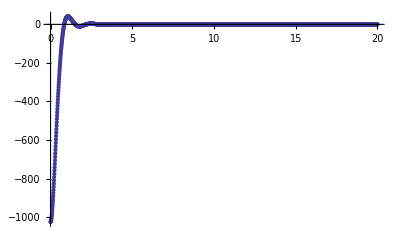

```mathematica
ListPlot[data,PlotRange->Full]
```

```mathematica
Export["/tmp/cs.in",data,"Table"];
```

```mathematica
SystemOpen["/tmp/cs.in"]
```

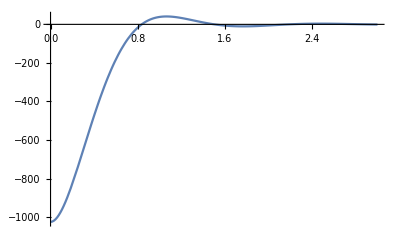

```mathematica
Quiet@Plot[4Pi*NIntegrate[ϕa[r]*r^2*Sin[k*r]/(k*r),{r,0,Infinity}],{k,0,3},PerformanceGoal->"Speed"]
```